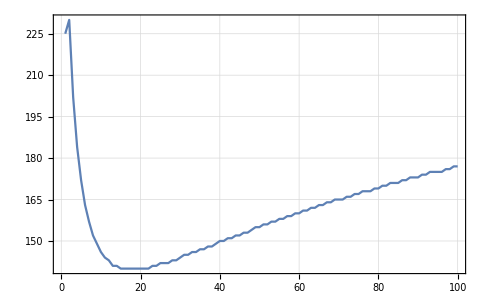
{-Graphics-,{15,140}}

{16,120}

```mathematica
T[max_]:=Module[{},{t,n}={0,max};
{m,p,c,k,g}={初始,产出,成本,系数,目标}={200,5,90,2,2000+45n};
While[n>0,{a,b}=QuotientRemainder[m,c];
p=p+k a;m=b+p;n-=a;t++];t+Ceiling[(g-m)/p]];
ans={#,T@#}&/@Range[100];
{ListLinePlot[ans,PlotTheme->"Detailed"],SortBy[ans, Last][[1]]}
```

```mathematica
data=BlockRandom[
SeedRandom[Method->{"MKL", Method->"Sobol"}];RandomReal[1,{1000}]];
```

```mathematica
CoefficientList[Product[1+k x,{k,0,#}],x]&/@Range@10;
Grid[%,Alignment->Left,Background->{{{Lighter@LightBlue,Lighter@LightGreen}}},Dividers->{True,All}]
```

1 | 1 |  |  |  |  |  |  |  |  | 
1 | 3 | 2 |  |  |  |  |  |  |  | 
1 | 6 | 11 | 6 |  |  |  |  |  |  | 
1 | 10 | 35 | 50 | 24 |  |  |  |  |  | 
1 | 15 | 85 | 225 | 274 | 120 |  |  |  |  | 
1 | 21 | 175 | 735 | 1624 | 1764 | 720 |  |  |  | 
1 | 28 | 322 | 1960 | 6769 | 13132 | 13068 | 5040 |  |  | 
1 | 36 | 546 | 4536 | 22449 | 67284 | 118124 | 109584 | 40320 |  | 
1 | 45 | 870 | 9450 | 63273 | 269325 | 723680 | 1172700 | 1026576 | 362880 | 
1 | 55 | 1320 | 18150 | 157773 | 902055 | 3416930 | 8409500 | 12753576 | 10628640 | 3628800

```mathematica
ContourPlot
```

```mathematica
ArrayPlot
```

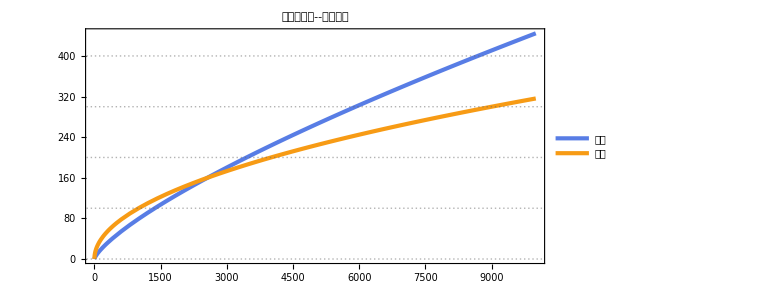

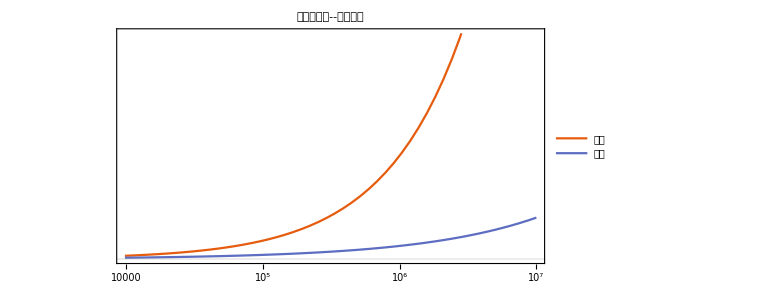

```mathematica
Plot[{10(x/10)^0.75/4,10(x/10)^0.5},{x,0,10000},AspectRatio->1/2,ImageSize->Large,PlotLegends->{"原版","改版"},PlotTheme->"Business",PlotLabel->"攻击血量积--战斗力图"]
Plot[{(x)^0.75/4,(x)^0.5},{x,0,10000000},AspectRatio->1/2,ImageSize->Large,PlotLegends->{"原版","改版"},PlotTheme->"Scientific",PlotLabel->"攻击血量积--战斗力图",ScalingFunctions->{"Log"}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sdfsdf.png"]]]
```

```mathematica
LogPlot
```

```mathematica
foo[p_,q_]:=Join[Flatten[ConstantArray@@@Table[{n,Ceiling[p/n]},{n,1,p}]],p+Ceiling@Accumulate[Range[q]]]
```

```mathematica
Product[(1-t/100)^12,{t,0,n}]
```

```mathematica
Table[{n,Product[(1-0.001t)^12,{t,0,n}]},{n,1,20}]//TableForm
```

1 | 0.988066
2 | 0.964611
3 | 0.930453
4 | 0.88676
5 | 0.834994
6 | 0.776819
7 | 0.714021
8 | 0.648412
9 | 0.581748
10 | 0.515653
11 | 0.451557
12 | 0.390657
13 | 0.333889
14 | 0.281919
15 | 0.235158
16 | 0.193776
17 | 0.15774
18 | 0.126847
19 | 0.100765
20 | 0.0790718